# Lección 2 -Funciones

## Funciones relacionadas a números

Resultados exactos

```mathematica
1/2+1/3
```

5/6

Aproximación numérica de una expresión

```mathematica
N[1/2+1/3]
```

0.833333

Uso de decimales

```mathematica
1/2.+1/3
```

0.833333

Número de precisión arbitraria

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

Aproxima el número

```mathematica
N[2^1000]
```

1.07151×10^301

Notación científica

```mathematica
2.7*^6
```

2.7×10^6

Constantes matemáticas como π

```mathematica
{Pi,N[π]}
```

{π,3.14159}

Precisión de 250 dígitos

```mathematica
N[Pi,250]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909

Números aleatorios

```mathematica
RandomReal[10]
```

8.10871

```mathematica
RandomReal[10,5]
```

{2.99517,6.03549,0.968052,3.52814,6.09826}

```mathematica
RandomReal[{20,30},5]
```

{28.9478,25.1533,21.559,23.7277,25.2266}

Números primos

```mathematica
Prime[100]
```

541

Raices cuadradas

```mathematica
{Sqrt[200],Sqrt[200.]}
```

{10 √2,14.1421}

Logaritmos

```mathematica
Log10[27.38]
```

1.43743

```mathematica
Log[ⅇ^2]
```

2

Gráficos con escala logarítmica

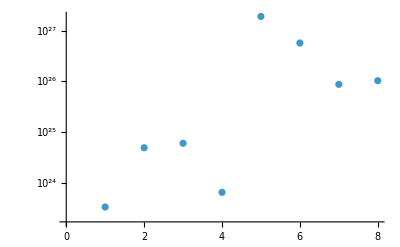

```mathematica
ListLogPlot[EntityClass["Planet",All]["Mass"]]
```

Valor absoluto

```mathematica
Abs[-3]
```

3

Redondeo

```mathematica
{Round[3.2],Round[3.4],Round[3.6],Round[3.9]}
```

{3,3,4,4}

Aritmética modular

```mathematica
Mod[70,60]
```

10

## Formas de aplicar funciones

Notación prefijo

```mathematica
f@x
```

f[x]

Cadena de aplicaciones

```mathematica
f@g@h@x
```

f[g[h[x]]]

```mathematica
ColorNegate@EdgeDetect@-Graphics-
```

-Graphics-

Notación posfijo

```mathematica
x//f
```

f[x]

Cadena de posfijo

```mathematica
x//f//g//h
```

h[g[f[x]]]

```mathematica
-Graphics-//EdgeDetect//ColorNegate
```

-Graphics-

Uso de posfijo

```mathematica
2Pi^3+1//N
```

63.0126

Aplicar a cada elemento

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
f[{1,2,3}]
```

f[{1,2,3}]

Encasillar cada variable

```mathematica
Framed/@{x,y,z}
```

{x,y,z}

Otro ejemplo

```mathematica
PieChart/@{{1,1,1,1,1,1,1},{1,1,1,4,4,4},{1,2,1,2,1,2}}
```

{-Graphics-,-Graphics-,-Graphics-}

Simbolos que funcionan de forma vectorizada

```mathematica
Prime[{10,100,1000,10000}]
```

{29,541,7919,104729}

```mathematica
Exp[{1,2,3,4}]
```

{ⅇ,ⅇ^2,ⅇ^3,ⅇ^4}

## Funciones puras

Blur de figuras

```mathematica
Blur/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

Define función pura con un parámetro

```mathematica
Blur[#,5]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

El # es un “slot” que recibe el argumento. El & indica lo que va antes es una función pura

```mathematica
Rotate[#,90Degree]&/@{"one","two","three"}
```

{one,two,three}

Ejemplos

```mathematica
StringLength[WikipediaData[#]]&/@{"apple","peach","pear"}
```

{38965,43133,12998}

```mathematica
Style[#,Hue[#/10],5*#]&/@IntegerDigits[2^100]
```

{1,2,6,7,6,5,0,6,0,0,2,2,8,2,2,9,4,0,1,4,9,6,7,0,3,2,0,5,3,7,6}

Función abstracta

```mathematica
f[#,x]&/@{a,b,c,d,e}
```

{f[a,x],f[b,x],f[c,x],f[d,x],f[e,x]}

Equivalencia de llamado de función

```mathematica
f[#]&/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

Número de slots son tantos como uno quiera

```mathematica
f[#,{x,#},{#,#}]&/@{a,b,c}//Column
```

f[a,{x,a},{a,a}]
f[b,{x,b},{b,b}]
f[c,{x,c},{c,c}]

Evaluación función pura

```mathematica
f[#,a]&  [x]
```

f[x,a]

```mathematica
f[#,a]&/@{x,y,z}
```

{f[x,a],f[y,a],f[z,a]}

## Tests y condicionales

Tests elementales

```mathematica
2+2==4
```

True

```mathematica
2*2>5
```

False

“Branching” con condicional

```mathematica
If[2+2==4,x,y]
```

x

Función pura con condicional

```mathematica
If[#<4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,y,y,y}

```mathematica
If[#≤ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,x,y,y,y}

```mathematica
If[#== 4,x,y]&/@{1,2,3,4,5,6,7}
```

{y,y,y,x,y,y,y}

```mathematica
If[#≠ 4,x,y]&/@{1,2,3,4,5,6,7}
```

{x,x,x,y,x,x,x}

Seleccionar elementos que pasen una condición

```mathematica
Select[{1,2,3,4,5,6,7},#>3&]
```

{4,5,6,7}

Funciones de testeo

```mathematica
Select[{1,2,3,4,5,6,7,8,9},EvenQ]
```

{2,4,6,8}

```mathematica
Select[Range[30],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29}

Combinar predicados lógicos

```mathematica
Select[{1,2,3,4,5,6,7},!(EvenQ[#]||#>4)&]
```

{1,3}

Palabras palindromas en inglés

```mathematica
Select[WordList[ ],StringReverse[#]==#&]
```

{a,aha,bib,bob,civic,dad,deed,did,dud,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,pop,pup,radar,refer,rotor,sis,tat,tenet,TNT,toot,tot,tut,wow}

Evaluación de pertenencia

```mathematica
MemberQ[{1,3,5,7},5]
```

True

Otros ejemplos

```mathematica
ImageInstanceQ[-Graphics-,LinguisticAssistant]
```

True

```mathematica
Select[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},GeoDistance[#,LinguisticAssistant]<LinguisticAssistant&]
```

{New York City,Chicago}

## Definir variables

Uso de %

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
%^2
```

{1,4,9,16,25,36,49,64,81,100}

Definir una variable

```mathematica
thing=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
thing
```

{1,2,3,4,5,6,7,8,9,10}

Opera con la variable

```mathematica
thing^2
```

{1,4,9,16,25,36,49,64,81,100}

Suprimir la salida

```mathematica
millionlist=Range[1000000];
```

Suma de elementos de la variable

```mathematica
Total[millionlist]
```

500000500000

Persistencia de variable

```mathematica
x=42
```

42

```mathematica
{x,y,z}
```

{42,y,z}

Borrar una variable

```mathematica
Clear[x]
```

```mathematica
{x,y,z}
```

{x,y,z}

Localizar una variable

```mathematica
Module[{x=Range[10]},x^2]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
x
```

x

Se puede localizar tantas variables como se requiera

```mathematica
Module[{x=Range[10],n=2},x^n]
```

{1,4,9,16,25,36,49,64,81,100}

Evaluación secuencial

```mathematica
x=Range[10];y=x^2;y=y+10000
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

Borrar los símbolos usados

```mathematica
Clear[x,y]
```

Secuencia dentro de Module

```mathematica
Module[{x,y},x=Range[10];y=x^2;y=y+10000]
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

```mathematica
{x,y}
```

{x,y}

## Valores inmediatos y “delayed”

Asignación inmediata

```mathematica
value=RandomColor[ ]
```

RGBColor[0.43968054884655694, 0.5274888616145352, 0.052023366982486996]

El resultado no cambia

```mathematica
value
```

RGBColor[0.43968054884655694, 0.5274888616145352, 0.052023366982486996]

En una asignación diferida el resultado no se genera inmediatamente

```mathematica
value:=RandomColor[ ]
```

```mathematica
value
```

RGBColor[0.9069279700779886, 0.1944344928680377, 0.5897902855922712]

Uso de := para expresiones que aún no tienen todos los valores requeridos

```mathematica
circles:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
```

```mathematica
n=6
```

6

Evaluación luego de asignar el valor faltante

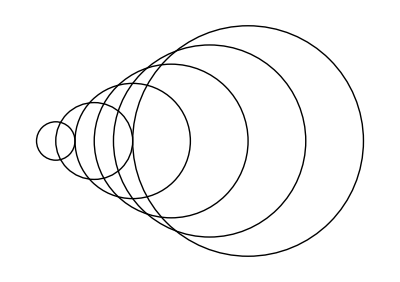

```mathematica
circles
```

## Define tus funciones

Definición básica de una función de un argumento

```mathematica
pinks[n_]:=Table[Pink,n]
```

```mathematica
pinks[4]
```

{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]}

```mathematica
pinks[8]
```

{RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5],RGBColor[1, 0.5, 0.5]}

Establecer definiciones

```mathematica
{f[Red],f[Yellow],f[Green],f[Orange],f[Magenta]}
```

{f[RGBColor[1, 0, 0]],f[RGBColor[1, 1, 0]],f[RGBColor[0, 1, 0]],f[RGBColor[1, 0.5, 0]],f[RGBColor[1, 0, 1]]}

```mathematica
f[Red]=1000;f[Green]=2000;
```

```mathematica
{f[Red],f[Yellow],f[Green],f[Orange],f[Blue]}
```

{1000,f[RGBColor[1, 1, 0]],2000,f[RGBColor[1, 0.5, 0]],f[RGBColor[0, 0, 1]]}

Funcionamiento de definiciones generales y específicas

```mathematica
f[x_]:=Framed[Column[{x,ColorNegate[x]}]]
```

```mathematica
f[Red]
```

1000

```mathematica
f[Blue]
```

RGBColor[0, 0, 1]
RGBColor[1., 1., 0.]

Definición recursiva del factorial

```mathematica
factorial[1]=1; factorial[n_Integer]:=n*factorial[n-1]
```

```mathematica
factorial[50]
```

30414093201713378043612608166064768844377641568960512000000000000

```mathematica
factorial[0.5]
```

factorial[0.5]

```mathematica
Factorial[50]
```

30414093201713378043612608166064768844377641568960512000000000000

Definición alternativa con If

```mathematica
factorial[n_Integer]:=If[n==1,1,n*factorial[n-1]]
```

```mathematica
factorial[5]
```

120

Elección adecuada del número de argumentos

```mathematica
plusminus[{x_,y_}]:={x+y,x-y}
```

```mathematica
plusminus[{4,1}]
```

{5,3}

```mathematica
plusminus[v_]:={v[[1]]+v[[2]],v[[1]]-v[[2]]}
```

```mathematica
plusminus[{4,1}]
```

{5,3}

Función que aplique a elementos con cierta estructura

```mathematica
lista = {a,Framed[b],c,Framed[{d,e}],100}
```

{a,b,c,{d,e},100}

```mathematica
highlight[Framed[x_]]:=Style[Labeled[x,"+"],20,Background->LightYellow]
```

```mathematica
highlight/@ lista
```

{highlight[a],b+,highlight[c],{d,e}+,highlight[100]}

Definición especializada

```mathematica
highlight[list_List]:=highlight/@list
```

```mathematica
highlight[lista]
```

{highlight[a],b+,highlight[c],{d,e}+,highlight[100]}

Definición adicional para un caso genérico

```mathematica
highlight[x_]:=Style[Rotate[x,-30Degree],20,Orange]
```

```mathematica
highlight[lista]
```

{a,b+,c,{d,e}+,100}

## With,Block y Module (opcional)

Reemplazo directo de variables

```mathematica
With[{x=Cos[3]},(x+1)/(x-1)+2]
```

2+(1+Cos[3])/(-1+Cos[3])

Localización por valor

```mathematica
Block[{$MaxPrecision=24,$MinPrecision=24},Sin[1`12]]
```

0.841470984807896506652502

```mathematica
{$MaxPrecision,$MinPrecision}
```

{∞,0}

Simbolos nuevos dentro de Module

```mathematica
Unique[x]
```

x$34921

Diferentes resultados por el scoping

```mathematica
f[1]:=x^2 

testModule[]:=Module[{x=5},f[1]]
testBlock[]:=Block[{x=5},f[1]]
```

```mathematica
testModule[]
```

x^2

```mathematica
testBlock[]
```

25

## Ejercicios

Capítulo 23:  1,3,4,10,13,14, +4

Capítulo 25:  1,4,5,9

Capítulo 26:  1,3,7,+1

Capítulo 28:  2,3,6,10, +2,+6

Capítulo 38: 2,3,5,7

Capítulo 39: 1,2

Capítulo 40:  2,4,6,8,9,10